I always enjoy reading the weekly Riddler puzzles from 538 (link). My background is not in statistics, but I enjoy the puzzles because they’re typically just the right amount of complexity to solve in a reasonable time frame and the topics are interesting and wide-ranging. When there is one involving sports, it’s even better.

Here’s the Riddler express from June 3rd 2021 discussing baseball perfect games:

How low would a batter’s chances of reaching base have to be for you to expect one perfect game per season? (You can make the following simplifying assumptions: All batters have the same chances of reaching base; at-bats are independent from each other; there are 30 MLB teams, and each club plays 162 games; and no games go into extra innings.)

My preferred computational tool is the Wolfram Language so I’ll take a stab at solving this Riddler using it.

First, let’s define some global constants based on what we are allowed to assume.

```mathematica
gamesPerYear=162;
teams=30;
numberOfInnings=9;
atBatsPerInning=3;
atBatsDuringAGame=numberOfInnings*atBatsPerInning;
```

Now, my preferred approach to a lot of these statistically based Riddler’s is to just simulate them. The primary reason is because I have very little actual formal training in statistics, but also because I believe that modern computers today combined with powerful computation languages, give us a very good way of solving these problems that previously had to be solved using pure mathematics.

So, we need a way of simulating a baseball season and to start we will need to create a distribution based on the on-base average. In this case, we can use EmpiricalDistribution and assign a weight based on the on-base average. The resulting output will be either a 1 when the batter gets on base, or a 0 when they do not.

```mathematica
createDist[onBasePct_]:=EmpiricalDistribution[{1-onBasePct,onBasePct}->{0,1}]
```

Simulating a full season requires us to randomly sample our on-base distribution for the total number of at bats that we can expect for every game played across each team. Then, to ensure we account for randomness correctly, because this is a simulation, we need to repeat this process a number of times. The more we perform a simulation, averaging the results, the better our prediction will be.

RandomVariate lets us sample our distribution a number of times and create nested arrays. In this case we simulate the number of at bats in a game for each team across an entire season 100 times. Then for each simulation we count the number of perfect games we have and take an average across the full number of season simulations.

```mathematica
numberOfSeasonSimulations=100;
```

```mathematica
simulateFullSeason[onBasePct_]:=Module[{dist,data,perfectGameCount},
	dist=createDist[onBasePct];
	data=RandomVariate[createDist[onBasePct],{
		numberOfSeasonSimulations,
		teams*gamesPerYear,
		atBatsDuringAGame
	}];
	perfectGameCount=Map[Count[x_/;AllTrue[x,EqualTo[0]]]]@data;
	N@Mean[perfectGameCount]
]
```

Simulating each season multiple times for various on-base averages let’s us see how the number of predicted perfect games in a season varies.

```mathematica
results=Table[{onBasePct,simulateFullSeason[onBasePct]},{onBasePct,0.1,0.4,0.01}]
```

{{0.1,280.39},{0.11,208.86},{0.12,154.05},{0.13,112.68},{0.14,80.32},{0.15,60.37},{0.16,43.14},{0.17,31.71},{0.18,23.1},{0.19,16.44},{0.2,11.88},{0.21,8.62},{0.22,6.67},{0.23,4.08},{0.24,2.91},{0.25,2.07},{0.26,1.43},{0.27,0.91},{0.28,0.59},{0.29,0.42},{0.3,0.38},{0.31,0.19},{0.32,0.16},{0.33,0.09},{0.34,0.08},{0.35,0.02},{0.36,0.02},{0.37,0.03},{0.38,0.02},{0.39,0.},{0.4,0.01}}

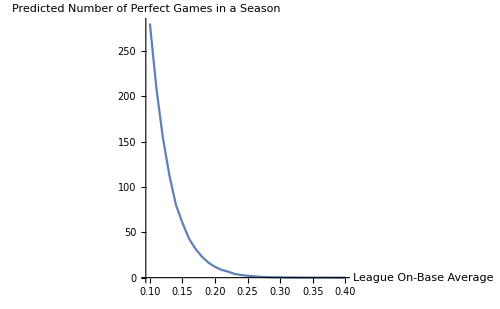

```mathematica
ListLinePlot[
	results,
	AxesLabel->{"League On-Base Average","Predicted Number of\nPerfect Games in a Season"},
	ImageSize->500
]
```

And finally, using the results we can calculate the required on-base average that would lead to one perfect game per season

```mathematica
FindRoot[Interpolation[results][onBasePct]==1,{onBasePct,0.2}]
```

{onBasePct→0.268269}